```mathematica
CellPrint[Cell["Directory","Section"]]
CellPrint[Cell["Main code & XZ independent noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"general_codes.nb"],Appearance->"DialogBox"]
CellPrint[Cell["DATA & code definitions :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"data_summary.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depoloarizing Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Approxiating polynomials:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"approximating_polynomials.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depolarizing noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ (symmetric) noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise_ME.nb"],Appearance->"DialogBox"]
SetDirectory[NotebookDirectory[]]
```

## Directory

Main code & XZ independent noise:

DATA & code definitions :

Depoloarizing Noise:

XZ uneven Noise:

Approxiating polynomials:

Depolarizing noise with Measurement error :

XZ (symmetric) noise with Measurement error :

XZ uneven noise with Measurement error :

/Users/naomi/Dropbox/&Projects/Small codes

## Additional code for noise model

```mathematica
countXZunevenErrors[Q_]:=Count[#,-1]&/@Thread@Partition[Q,2]

polynomialXZuneven[tally_,nQ_]:=Plus@@((#[[2]](px)^(#⟦1,1⟧)(1-px)^(nQ-#⟦1,1⟧)(pz)^(#⟦1,2⟧)(1-pz)^(nQ-#⟦1,2⟧))&/@tally)

testCodeXZuneven[code_,testErrors_:5]:=Module[{S,L,nQubits,sLists,sVecs,sGroup,errCount,lLists,lGroup,lVecs,Qstates,syndromes},

{nQubits,S,L}=code;

(* generate the stabilizer lists and qubit array *)
sLists = createStabilizerLists[S]; (* for measurement *)
sVecs = createStabilizerVectors[S,nQubits];(* for applying operators *)
sGroup =Times@@#&/@ Subsets[sVecs,All];

(* generate the logical operators *)
lLists = createStabilizerLists[L];
lVecs = createStabilizerVectors[L,nQubits];
lGroup=Times@@#&/@Subsets[lVecs,All];

{syndromes,Qstates}=generateSyndromes[sLists,sGroup,nQubits,testErrors];
errCount = countSyndromeErrors[#,lGroup,sGroup,countXZunevenErrors]&/@Qstates;
{syndromes,errCount}

]

testCodeXZunevenSlow[code_,testErrors_:5]:=Module[{S,L,nQubits,sLists,sVecs,sGroup,errCount,lLists,lGroup,lVecs,Qstates,syndromes,x,i},

{nQubits,S,L}=code;

(* generate the stabilizer lists and qubit array *)
sLists = createStabilizerLists[S]; (* for measurement *)
sVecs = createStabilizerVectors[S,nQubits];(* for applying operators *)
sGroup =Times@@#&/@ Subsets[sVecs,All];

(* generate the logical operators *)
lLists = createStabilizerLists[L];
lVecs = createStabilizerVectors[L,nQubits];
lGroup=Times@@#&/@Subsets[lVecs,All];

Print["generated operators"];
{syndromes,Qstates}=generateSyndromes[sLists,sGroup,nQubits,testErrors];
Print["got syndromes"];
Print[Length[Qstates]];
errCount={};
For[i=1,i<=Length[Qstates],i++,
x=countSyndromeErrors[Qstates[[i]],lGroup,sGroup,countXZunevenErrors];
errCount =Append[errCount,x];
If[Mod[i,100]==0,Print[i]];
(*errCount = countSyndromeErrors[#,lGroup,sGroup,countXZunevenErrors]&/@Qstates;*)
];

{syndromes,errCount}
]

checkResultsValidXZuneven[polynomial_,nQ_]:=Module[{sum},
sum=FullSimplify[Plus@@Flatten@(polynomialXZuneven[#,nQ]&/@#&/@polynomial)];
Print[sum];
If[sum==1,Print["Results checked: elements sum to 1"],Print[{"ERROR: elements don't sum to 1 ",sum}];];
]

XZunevenData[function_,a_,nQ_,results_]:=Module[{polynomials,pxval,pzval,p},
(* generates a table of data over the range of p for a fixed value of a, 
px = a pz *)
{pxval,pzval}=pxpz[a,p]; (* px = α pz *)
polynomials = polynomialXZuneven[#,nQ]&/@#&/@results;
polynomials = polynomials/.{px->pzval,pz->pxval};
Table[{p,function[p,polynomials]},{p,0.001,0.2,0.01}]
]

(*plotResultsXZuneven[results_,nQ_,function_,a_:1,color_:1,label_:None,fill_:False]:=Module[{polynomials,ep,test,pzval,pxval,b},
(* makes a single plot of a function of the results data for a fixed value of a, where px = a pz *)
ep= XZunevenData[function,a,nQ,results];
ListPlot[ep,Joined->True,PlotStyle->ColorData[97,color],PlotLegends->{label}]
]

plotResultsXZunevenRange[results_,nQ_,function_,color_:1,label_:None]:=Module[{polynomials,ep,test,pzval,pxval,amin,amax,fMin,fMax,plot1,plot2},
(* plots the region enclosed by the set of variables px and pz *)
amin=0.0000001;
amax=10000000;

fMin=XZunevenData[function,amin,nQ,results];
fMax=XZunevenData[function,amax,nQ,results];

plot1=ListPlot[{fMin,fMax},Joined->True,PlotStyle->ColorData[97,color],PlotLegends->{label},Filling->{1->{2}}];

plot2=ListPlot[XZunevenData[function,1,nQ,results],Joined->True,PlotStyle->{Dotted,ColorData[97,1]}];

Show[plot1,plot2,
Plot[(1-p),{p,0,1},PlotStyle->{Black,Dashed}],
Frame->True,FrameLabel->{"p","success rate"},LabelStyle->Medium]
]

*)


successRate[pVal_,polynomials_]:=Module[{poly},
poly=polynomials/.{p->pVal};
Plus@@(Max[#]&/@poly)
]

truncatePolynomialsXZ[poly_,nmax_]:=Select[#,Plus@@(#[[1]])<nmax&]&/@#&/@poly
```

## Generate polynomials

```mathematica
testCodeXZuneven[codeP5]>> "data/xzUnevenP5.txt"
```

```mathematica
testCodeXZuneven[codeP6]>> "data/xzUnevenP6.txt"
```

```mathematica
testCodeXZuneven[codeP7]>> "data/xzUnevenP7a.txt"
```

```mathematica
testCodeXZuneven[codeP7b]>> "data/xzUnevenP7b.txt"
```

```mathematica
testCodeXZuneven[codeP8]>> "data/xzUnevenP8.txt"
```

```mathematica
testCodeXZuneven[codeP8b]>> "data/xzUnevenP8b.txt"
```

```mathematica
testCodeXZuneven[codeP9]>> "data/xzUnevenP9.txt"
```

```mathematica
testCodeXZuneven[codeP9b]>>"data/xzUnevenP9b.txt";
```

```mathematica
testCodeXZuneven[codeP13,7]>> "data/xzUnevenP13.txt"
```

```mathematica
testCodeXZuneven[codeC7]>> "data/xzUnevenC7.txt"
```

```mathematica
testCodeXZuneven[codeC11]>> "data/xzUnevenC11.txt"
```

## generate data

### 5 qubit planar

```mathematica
{syndromeXZunevenP5,polyXZunevenP5} =<<"data/xzUnevenP5.txt";
checkResultsValidXZuneven[polyXZunevenP5,5]
```

1

Results checked: elements sum to 1

```mathematica
XZunevenData[successRate,1,5,polyXZunevenP5]>>"data/xzUneven_P5_a1.txt";
```

```mathematica
XZunevenData[successRate,0.0000001,5,polyXZunevenP5]>>"data/xzUneven_P5_a0";
```

```mathematica
XZunevenData[successRate,10000,5,polyXZunevenP5]>>"data/xzUneven_P5_a10000";
```

### 6 qubit planar

```mathematica
{syndromeXZunevenP6,polyXZunevenP6} =<<"data/xzUnevenP6.txt";
checkResultsValidXZuneven[polyXZunevenP6,6]
```

```mathematica
XZunevenData[successRate,1,6,polyXZunevenP6]>>"data/xzUneven_P6_a1.txt";
```

```mathematica
XZunevenData[successRate,0.0000001,6,polyXZunevenP6]>>"data/xzUneven_P6_a0";
```

```mathematica
XZunevenData[successRate,10000,6,polyXZunevenP6]>>"data/xzUneven_P6_a10000";
```

### 7a qubit planar

```mathematica
{syndromeXZunevenP7a,polyXZunevenP7a} =<<"data/xzUnevenP7a.txt";
checkResultsValidXZuneven[polyXZunevenP7a,7]
```

1

Results checked: elements sum to 1

```mathematica
XZunevenData[successRate,1,7,polyXZunevenP7a]>>"data/xzUneven_P7a_a1.txt";
```

```mathematica
XZunevenData[successRate,0.0000001,7,polyXZunevenP7a]>>"data/xzUneven_P7a_a0";
```

```mathematica
XZunevenData[successRate,10000,7,polyXZunevenP7a]>>"data/xzUneven_P7a_a10000";
```

### 7(b) qubit planar

```mathematica
{syndromeXZunevenP7b,polyXZunevenP7b} =<<"data/xzUnevenP7b.txt";
checkResultsValidXZuneven[polyXZunevenP7b,7]
```

1

Results checked: elements sum to 1

```mathematica
XZunevenData[successRate,1,7,polyXZunevenP7b]>>"data/xzUneven_P7b_a1.txt";
```

```mathematica
XZunevenData[successRate,0.0000000001,7,polyXZunevenP7b]>>"data/xzUneven_P7b_a0";
```

```mathematica
XZunevenData[successRate,1000000,7,polyXZunevenP7b]>>"data/xzUneven_P7b_a10000";
```

### 8 qubit planar

```mathematica
{syndromeXZunevenP8,polyXZunevenP8} =<<"data/xzUnevenP8.txt";
checkResultsValidXZuneven[polyXZunevenP8,8]
```

1

Results checked: elements sum to 1

```mathematica
XZunevenData[successRate,1,8,polyXZunevenP8]>>"data/xzUneven_P8_a1.txt";
```

```mathematica
XZunevenData[successRate,0.0000001,8,polyXZunevenP8]>>"data/xzUneven_P8_a0";
```

```mathematica
XZunevenData[successRate,10000,8,polyXZunevenP8]>>"data/xzUneven_P8_a10000";
```

### 8(b) qubit planar

```mathematica
{syndromeXZunevenP8b,polyXZunevenP8b} =<<"data/xzUnevenP8b.txt";
checkResultsValidXZuneven[polyXZunevenP8b,8]
```

1

Results checked: elements sum to 1

```mathematica
XZunevenData[successRate,1,8,polyXZunevenP8b]>>"data/xzUneven_P8b_a1.txt";
```

```mathematica
XZunevenData[successRate,0.0000001,8,polyXZunevenP8b]>>"data/xzUneven_P8b_a0";
```

```mathematica
XZunevenData[successRate,10000,8,polyXZunevenP8b]>>"data/xzUneven_P8b_a10000";
```

### 9 qubit planar

```mathematica
{syndromeXZunevenP9,polyXZunevenP9} =<<"data/xzUnevenP9.txt";
checkResultsValidXZuneven[polyXZunevenP9,9]
```

```mathematica
XZunevenData[successRate,1,9,polyXZunevenP9]>>"data/xzUneven_P9_a1.txt";
XZunevenData[successRate,0.0000001,9,polyXZunevenP9]>>"data/xzUneven_P9_a0";
XZunevenData[successRate,10000,9,polyXZunevenP9]>>"data/xzUneven_P9_a10000";
```

### 9(b) qubit planar

```mathematica
{syndromeXZunevenP9b,polyXZunevenP9b} =<<"data/xzUnevenP9b.txt";
checkResultsValidXZuneven[polyXZunevenP9b,9]
```

```mathematica
XZunevenData[successRate,1,9,polyXZunevenP9b]>>"data/xzUneven_P9b_a1";
XZunevenData[successRate,0.0000001,9,polyXZunevenP9b]>>"data/xzUneven_P9b_a0";
XZunevenData[successRate,10000,9,polyXZunevenP9b]>>"data/xzUneven_P9b_a10000";
```

### 13 qubit planar

```mathematica
{syndromeXZunevenP13,polyXZunevenP13} =<<"data/xzUnevenP13.txt";
```

```mathematica
checkResultsValidXZuneven[polyXZunevenP13,13]
```

1

Results checked: elements sum to 1

```mathematica
polyXZunevenP13truncated=truncatePolynomialsXZ[polyXZunevenP13,10];
```

```mathematica
XZunevenData[successRate,1,13,polyXZunevenP13truncated]>>"data/xzUneven_P13_a1.txt";
```

```mathematica
XZunevenData[successRate,0.0000001,13,polyXZunevenP13truncated]>>"data/xzUneven_P13_a0";
```

```mathematica
XZunevenData[successRate,10000,13,polyXZunevenP13truncated]>>"data/xzUneven_P13_a10000";
```

### 7 qubit color

```mathematica
{syndromeXZunevenC7,polyXZunevenC7} =<<"data/xzUnevenC7.txt";
checkResultsValidXZuneven[polyXZunevenC7,7]

XZunevenData[successRate,1,7,polyXZunevenC7]>>"data/xzUneven_C7_a1.txt";
XZunevenData[successRate,0.0000001,7,polyXZunevenC7]>>"data/xzUneven_C7_a0";
XZunevenData[successRate,10000,7,polyXZunevenC7]>>"data/xzUneven_C7_a10000";
```

1

Results checked: elements sum to 1

### 11 qubit color

```mathematica
{syndromeXZunevenC11,polyXZunevenC11} =<<"data/xzUnevenC11.txt";
checkResultsValidXZuneven[polyXZunevenC11,11]

XZunevenData[successRate,1,11,polyXZunevenC11]>>"data/xzUneven_C11_a1.txt";
XZunevenData[successRate,0.0000001,11,polyXZunevenC11]>>"data/xzUneven_C11_a0";
XZunevenData[successRate,10000,11,polyXZunevenC11]>>"data/xzUneven_C11_a10000";
```

## Plots

```mathematica
plotDataXZuneven[d1_,d2_,d3_,filling_:{1->{2}}]:=Module[{plot1},
plot1=ListPlot[{d1,d2,d3},Joined->True,PlotStyle->{
Directive[Dotted,ColorData[97,1]],
Directive[ColorData[97,1],Dashing[0]],
Directive[Dotted,ColorData[97,1]]},Filling->filling];
plot1=Show[plot1,
Plot[(1-p),{p,0,1},PlotStyle->{Black,Dashed}],
Frame->True,FrameLabel->{"p","success rate"},LabelStyle->Medium];

Show[plot1,LabelStyle->20,FrameTicks->{{{0.7,0.8,0.9,1},None},{Automatic,None}},AspectRatio->0.9]
]
```

## 5 qubit planar

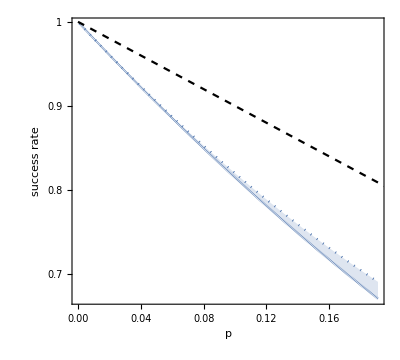

```mathematica
xzUnevenP5a1=<<"data/xzUneven_P5_a1.txt";
xzUnevenP5a0=<<"data/xzUneven_P5_a0";
xzUnevenP5a10000=<<"data/xzUneven_P5_a10000";

plotDataXZuneven[xzUnevenP5a0,xzUnevenP5a1,xzUnevenP5a10000]
```

## 6 qubit planar

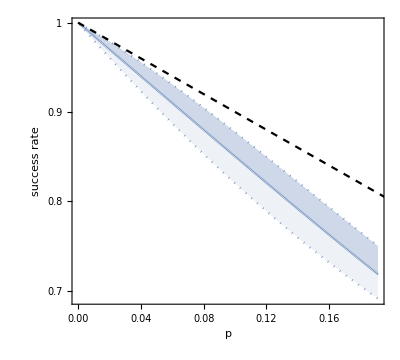

```mathematica
xzUnevenP6a1=<<"data/xzUneven_P6_a1.txt";
xzUnevenP6a0=<<"data/xzUneven_P6_a0";
xzUnevenP6a10000=<<"data/xzUneven_P6_a10000";

plotDataXZuneven[xzUnevenP6a0,xzUnevenP6a1,xzUnevenP6a10000,
{3->{{2},Directive[ColorData[97,1],Opacity[0.3]]},
2->{{1},Directive[ColorData[97,1],Opacity[0.1]]}}
]
```

## 7 qubit Planar Codes

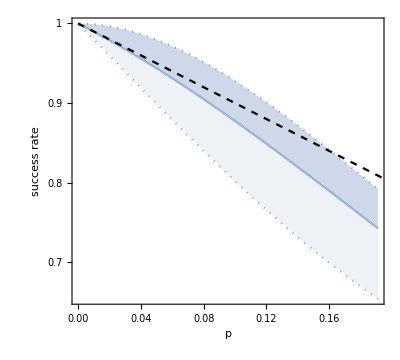

```mathematica
xzUnevenP7aa1=<<"data/xzUneven_P7a_a1.txt";
xzUnevenP7aa0=<<"data/xzUneven_P7a_a0";
xzUnevenP7aa10000=<<"data/xzUneven_P7a_a10000";

plotDataXZuneven[xzUnevenP7aa0,xzUnevenP7aa1,xzUnevenP7aa10000,
{3->{{2},Directive[ColorData[97,1],Opacity[0.3]]},
2->{{1},Directive[ColorData[97,1],Opacity[0.1]]}}
]
```

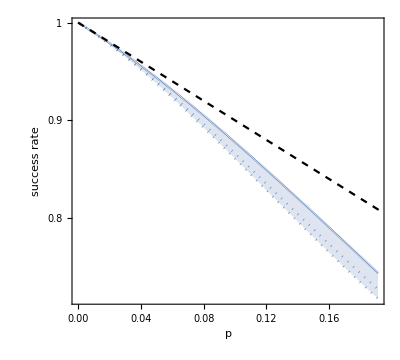

```mathematica
xzUnevenP7ba1=<<"data/xzUneven_P7b_a1.txt";
xzUnevenP7ba0=<<"data/xzUneven_P7b_a0";
xzUnevenP7ba10000=<<"data/xzUneven_P7b_a10000";

plotDataXZuneven[xzUnevenP7ba0,xzUnevenP7ba1,xzUnevenP7ba10000,{3->{2}}]
```

## 8 qubit surface Code

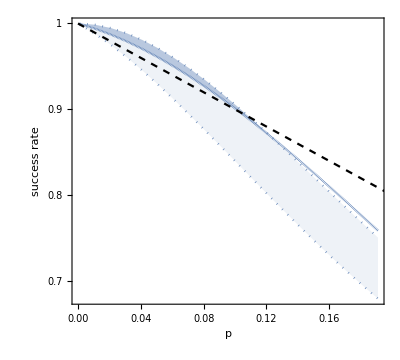

```mathematica
xzUnevenP8a1=<<"data/xzUneven_P8_a1.txt";
xzUnevenP8a0=<<"data/xzUneven_P8_a0";
xzUnevenP8a10000=<<"data/xzUneven_P8_a10000";

plotDataXZuneven[xzUnevenP8a0,xzUnevenP8a1,xzUnevenP8a10000,
{1->{{2},{None,Directive[ColorData[97,1],Opacity[0.2]]}},
3->{{1},Directive[ColorData[97,1],Opacity[0.1]]}}
]
```

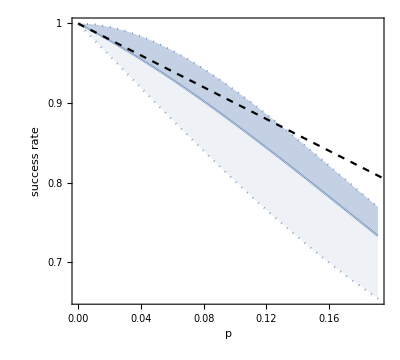

```mathematica
xzUnevenP8ba1=<<"data/xzUneven_P8b_a1.txt";
xzUnevenP8ba0=<<"data/xzUneven_P8b_a0";
xzUnevenP8ba10000=<<"data/xzUneven_P8b_a10000";

plotDataXZuneven[xzUnevenP8ba0,xzUnevenP8ba1,xzUnevenP8ba10000,
{3->{{2},{None,Directive[ColorData[97,1],Opacity[0.2]]}},
2->{{1},Directive[ColorData[97,1],Opacity[0.1]]}}
]
```

## 9 qubit surface Code

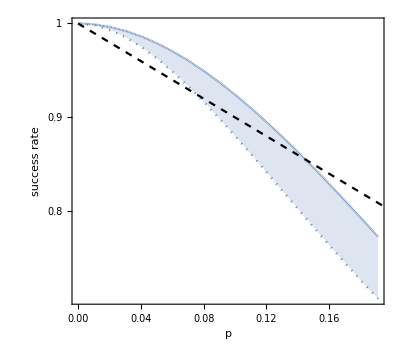

```mathematica
xzUnevenP9a1=<<"data/xzUneven_P9_a1.txt";
xzUnevenP9a0=<<"data/xzUneven_P9_a0";
xzUnevenP9a10000=<<"data/xzUneven_P9_a10000";

plotDataXZuneven[xzUnevenP9a0,xzUnevenP9a1,xzUnevenP9a10000]
```

### 9b A differnt code...

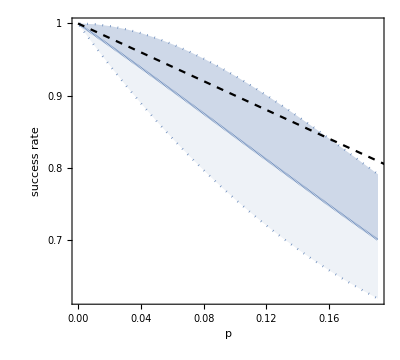

```mathematica
xzUnevenP9ba1=<<"data/xzUneven_P9b_a1";
xzUnevenP9ba0=<<"data/xzUneven_P9b_a0";
xzUnevenP9ba10000=<<"data/xzUneven_P9b_a10000";

plotDataXZuneven[xzUnevenP9ba0,xzUnevenP9ba1,xzUnevenP9ba10000,
{3->{{2},Directive[ColorData[97,1],Opacity[0.3]]},
2->{{1},Directive[ColorData[97,1],Opacity[0.1]]}}]
```

## 13 qubit surface

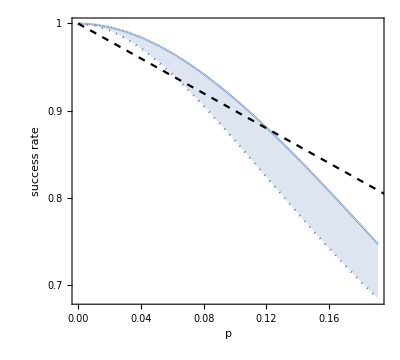

```mathematica
xzUnevenP13a1=<<"data/xzUneven_P13_a1.txt";
xzUnevenP13a0=<<"data/xzUneven_P13_a0";
xzUnevenP13a10000=<<"data/xzUneven_P13_a10000";

plotDataXZuneven[xzUnevenP13a0,xzUnevenP13a1,xzUnevenP13a10000]
```

## 7 qubit color

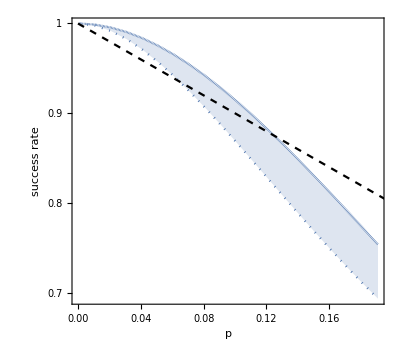

```mathematica
xzUnevenC7a1=<<"data/xzUneven_C7_a1.txt";
xzUnevenC7a0=<<"data/xzUneven_C7_a0";
xzUnevenC7a10000=<<"data/xzUneven_C7_a10000";

plotDataXZuneven[xzUnevenC7a0,xzUnevenC7a1,xzUnevenC7a10000]
```

## 11 qubit color

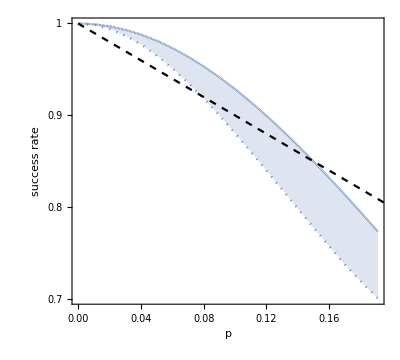

```mathematica
xzUnevenC11a1=<<"data/xzUneven_C11_a1.txt";
xzUnevenC11a0=<<"data/xzUneven_C11_a0";
xzUnevenC11a10000=<<"data/xzUneven_C11_a10000";

plotDataXZuneven[xzUnevenC11a0,xzUnevenC11a1,xzUnevenC11a10000]
```

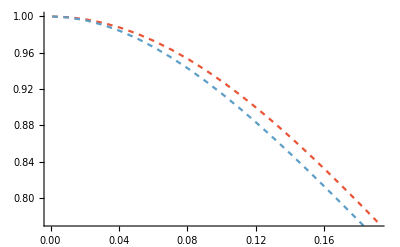

```mathematica
Show[ListPlot[#[[1]],Joined->True,PlotStyle->Directive[ColorData[97,#[[2]]],Dashing[0.01]]]&/@{{xzUnevenC11a1,11},{xzUnevenC7a1,7}}]
```